# Create training data set

Create 25.000 images 256 x 256 using the first ten Zernike polynomials with different levels of Gaussian
white noise (standard deviation is set from 0 to 1.5) and speckle noise. Then generate the
corresponding wrapped phase data according to Eq.(8).φ(x,y)=angle (exp(1i×φ(x,y))).

```mathematica
pthout="/home/jan/Desktop/UnwrappingPhase/Training/add_noise_2";
nDatasets=2000;
```

```mathematica
SeedRandom[0];
```

```mathematica
zernike2d[n_,m_,{x_,y_}]:=ZernikeR[n,m,Norm[{x,y}]]If[m<0,Sin[m #],Cos[m #]]&@ArcTan[x,y];
```

```mathematica
getnm[j_]:=Switch[j,
0,{0,0},
1,{1,-1},
2,{1,1},
3,{2,-2},
4,{2,0},
5,{2,2},
6,{3,-3},
7,{3,-1},
8,{3,1},
9,{3,3},
_,{0,0}
]
```

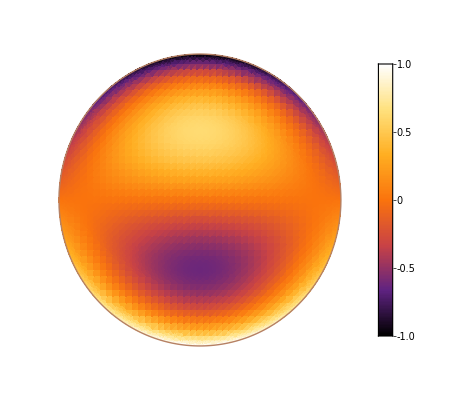

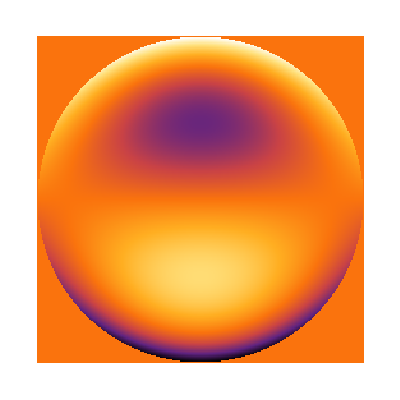

```mathematica
j=RandomInteger[{0,9}];
{n,m} =getnm[j];
DensityPlot[zernike2d[n,m,{x,y}],{x,-1.12,1.12},{y,-1.12,1.12},Exclusions-> None,PlotLegends-> Automatic,ColorFunction->"SunsetColors",RegionFunction:>(#1^2+#2^2≤1&),PlotPoints->50,BoundaryStyle->Black,Frame->False]

data=Table[If[Norm[{x,y}]<1,zernike2d[n,m,{x,y}],0.0],{x,Subdivide[-1.0,1,256-1]},{y,Subdivide[-1.0,1,256-1]}]ᵀ;
ArrayPlot[data,ColorFunction->"SunsetColors"]
```

```mathematica
(*additiveNoiseStd = RandomReal[{0,1.5}]
multiplicativeNoiseStd = RandomReal[{0,1.5}]*)
```

```mathematica
If[!DirectoryQ@#,CreateDirectory[#]]&@pthout;
If[!DirectoryQ@#,CreateDirectory[#]]&@FileNameJoin[{pthout,"unwrap"}];
If[!DirectoryQ@#,CreateDirectory[#]]&@FileNameJoin[{pthout,"wrap"}];
If[!DirectoryQ@#,CreateDirectory[#]]&@FileNameJoin[{pthout,"k"}];
Do[
j=RandomInteger[{0,9}];
data=ConstantArray[0,{256,256}];
Do[
{n,m} =getnm[j];
c=RandomReal[{0.0,10.0}];
data+=c Table[If[Norm[{x,y}]<1,zernike2d[n,m,{x,y}],0.0],{x,Subdivide[-1.0,1,256-1]},{y,Subdivide[-1.0,1,256-1]}]ᵀ;
,{j,0,9}
];
dataWrap=Mod[data,2π];
kxy=Round[(data-dataWrap)/(2.0π)];
dataWrapNoise=Mod[data+RandomVariate[NormalDistribution[0,2],{256,256}],2π];

(** export image data in binary hdf5 format **)
Export[FileNameJoin[{pthout,"unwrap","unwrap_"<>IntegerString[i,10,IntegerLength[nDatasets]+1]<>".hdf5"}],data,"HDF5"];
Export[FileNameJoin[{pthout,"wrap","wrap_"<>IntegerString[i,10,IntegerLength[nDatasets]+1]<>".hdf5"}],dataWrapNoise,"HDF5"];
Export[FileNameJoin[{pthout,"k","k_"<>IntegerString[i,10,IntegerLength[nDatasets]+1]<>".hdf5"}],kxy,"HDF5"];
,{i,1,nDatasets}];

p1=ArrayPlot[data,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{-10,30}];
p2=ArrayPlot[dataWrap,ColorFunction->"SunsetColors",PlotLegends->Automatic];
p3=ArrayPlot[kxy,ColorFunction->"SunsetColors",PlotLegends->Automatic];
p4=ArrayPlot[dataWrap+kxy 2π,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{-10,30}];
p5=ArrayPlot[dataWrapNoise+kxy 2π,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{-10,30}];
p6=ArrayPlot[dataWrapNoise-(dataWrap),ColorFunction->"SunsetColors",PlotLegends->Automatic];
Grid[{{p1,p4,p5,p6}}]
Grid[{{p2,p3}}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics-